

```mathematica
Plot[Sin[x],{x,0,2*π}]
```

```mathematica
Manipulate[
Plot[Sin[t+x],{x,0,2*π}]
,{t,0,π}]
```

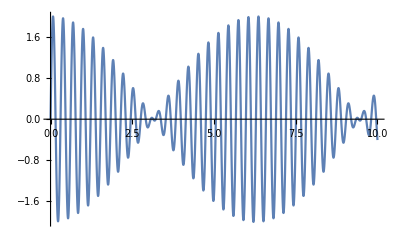

```mathematica
Plot[Sin[20*x]+Sin[21*x],{x,0,10}]
```

```mathematica
Manipulate[
Plot[Sin[20*x]+Sin[frequency*x],{x,0,10}]
,{frequency,20,24}]
```

```mathematica
Manipulate[
Plot[Sin[20*x]+boost*Sin[frequency*x],{x,0,10}]
,{frequency,20,24}
,{boost,{1,2,4}}]
```

```mathematica
Plot3D[Sqrt[x^2+y^2],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

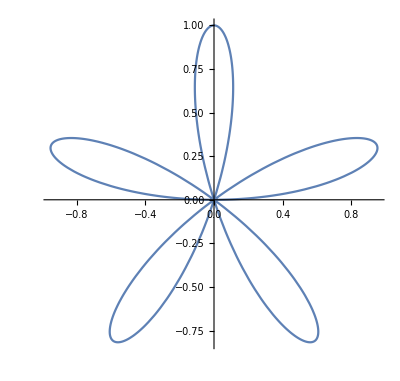

```mathematica
PolarPlot[Sin[5θ],{θ,0,π}]
```

```mathematica
SphericalPlot3D[Re[Sin[θ]Cos[θ]Exp[2I*φ]],{θ,0,π},{φ,0,2π}]
```

-Graphics3D-

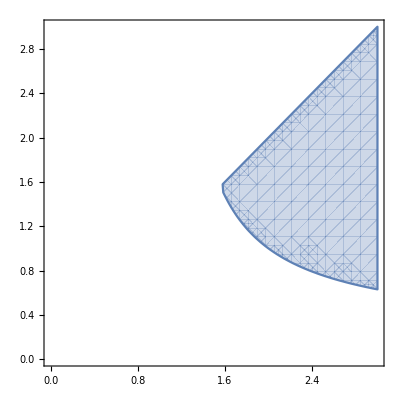

```mathematica
RegionPlot[x^y>2&&y<x,{x,0,3},{y,0,3}]
```

```mathematica
Animate[Plot[Sin[t-x],{x,0,10}],{t,0,10}]
```

```mathematica
Manipulate[Plot[x^2a+x*b,{x,-3,3}],{a,.1,3},{b,-3,3}]
```

```mathematica
Quit[];
```